## Periodic driven two coupled systems:

```mathematica
f=1/10; δ=1; ω0=1; d=1/10; β=1;
```

```mathematica
A1[ω_]:= f(ω0^2-ω+δ)/((ω0^2-ω^2)(ω0^2-ω+2 δ))
A2 [ω_]:= δ A1[ω]/(ω0^2-ω^2+δ)
```

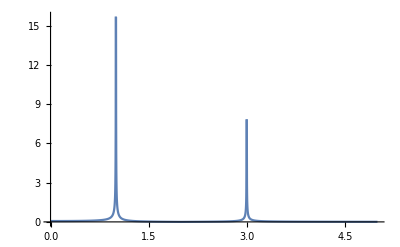

```mathematica
Plot[Abs[A1[ω]],{ω,0,5},PlotRange->All]
```

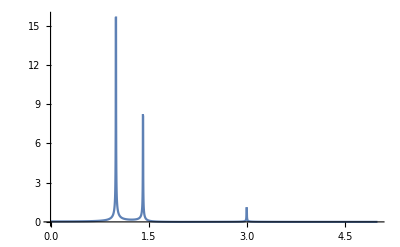

```mathematica
Plot[Abs[A2[ω]],{ω,0,5},PlotRange->All]
```

Solve the equation to get solution of the Amplitude:

```mathematica
Clear[A1,A2]
```

```mathematica
u1 = ω0^2-ω^2+δ+3 β/4 A1^2;
u2 = ω0^2-ω^2+δ+3 β/4 A2^2;
sol = Solve[{A1^2(u1^2+ d^2 ω^2)+(2 d^2 ω^2+ δ^2)A2^2-2 u1 u2 A2^2 == f^2 &&
A2^2(u2^2+d^2 ω^2)-δ^2 A1^2==0},{A1,A2}]
```

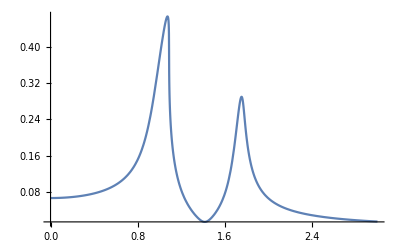

```mathematica
a1 =Plot[Evaluate[Abs[A1/.sol[[1]]]],{ω,0,3},PlotRange->All]
```

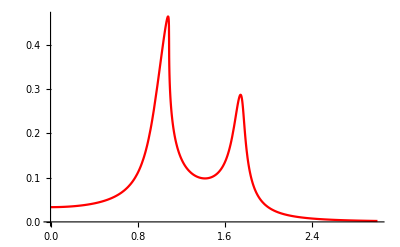

```mathematica
a2=Plot[Evaluate[Abs[A2 /. sol[[2]]]],{ω,0,3},PlotStyle->Red]
```

Amplitudes calculated using analytical expression:

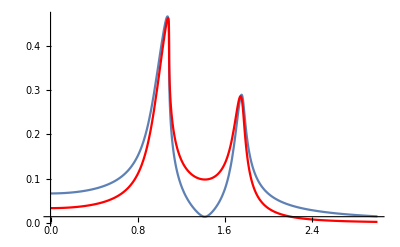

```mathematica
Show[{a1,a2}]
```